## September 30, 2020 Ground work for Starobinsky Potential and Scalar Potentials

### 1. Potential using constant V

#### First using Wiltshire eqn 3.56 from An Intro to Quantum Cosmology, simplify eqn 1 (3.56) below using, → k = 0, N = 1 and V = constant,

1/𝒩 d/dt((ϕ̇)/𝒩 )+3(ȧ)/(a(𝒩)^2)ϕ̇+1/2(dV/dϕ)=0

d/dt(ϕ̇ )+3(ȧ)/a ϕ̇+1/2(dV/dϕ)=0

```mathematica
(* Note that the derivative of a constant is 0 so the last term disappears *)
```

d^2/dt^2(ϕ )+3(ȧ)/a ϕ̇=0

#### Now using Wiltshire eqn 3.54 (the Friedmann eqn) from An Intro to QC, simplify eqn 3 (3.54) below,

H=1/2(-OverDot[aa]^2/𝒩^2+(a^3(ϕ̇)^2)/𝒩^2-ka+a^3 V)=0

1/2(-OverDot[aa]^2+a^3(ϕ̇)^2-ka+a^3 V)=0
1/2(-OverDot[aa]^2+a^3(ϕ̇)^2+a^3)=0

```mathematica
(* multiply both sides by 2/a *)
```

(-(a^·)^2+a^2(ϕ^·)^2+a^2)=0

#### Now we have our equations that we’ll plot, we just need the initial conditions. Below I solve for the initial conditions using Wiltshire’s exact solutions given in eqn 3.58 .

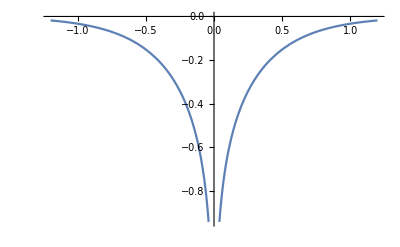

```mathematica
(* Below is a plot of ϕ[t] as given in solution 3.58 in Wiltshire *)
Plot[(1/3) Log[Abs[Tanh[(3/2) t]]],{t,-1.2,1.2}]
```

```mathematica
(* Notice that as t -> 0, ϕ -> -∞ and as t -> +∞, ϕ -> 0 *)

(* To find the initial condition for ϕ[t] use Wiltshire's exact solution 3.58 and plug in t -> 0 (I used 0.001) *)

(1/3) Log[Abs[Tanh[(3/2) (0.001)]]]
```

-2.16743

```mathematica
(* So we get the initial condition ϕ[0.001]=-2.16743 *)
```

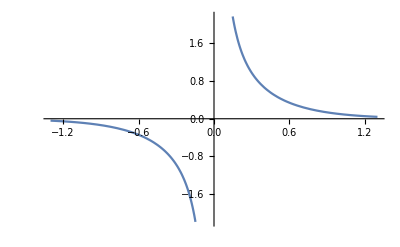

```mathematica
(* Below is a plot of the first derivative of ϕ[t] with respect to t *)
Plot[(Csch[(3 t)/2] Sech[(3 t)/2])/2,{t,-1.3,1.3}]
```

```mathematica
(* Notice that as t -> 0^+, ϕ' -> +∞ and as t -> 0^-, ϕ' -> -∞ *)
(* To find the initial condition for ϕ' use the above eqn for ϕ' and plug in t -> 0 (I used 0.001) *)

(Csch[(3 (0.001))/2] Sech[(3 (0.001))/2])/2
```

333.333

```mathematica
(* So we get the initial condition of ϕ'[0.001]=333.333 *)
```

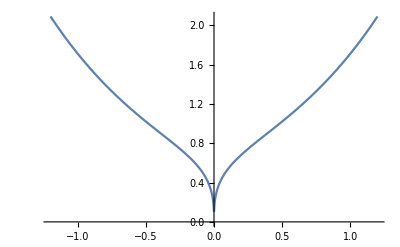

```mathematica
(* Below is a plot of a[t] as given in solution 3.58 in Wiltshire *)
Plot[Abs[Sinh[(3/2) t]]^(1/3) Abs[Cosh[(3/2) t]]^(1/3),{t,-1.2,1.2}]
```

```mathematica
(* Notice as t -> 0, a -> 0.1 or 0 (according to wolfram) *)
(* To find initial condition for a use the above eqn and plug in t -> 0 (I used 0.001) *)
Abs[Sinh[(3/2) (0.001)]]^(1/3) Abs[Cosh[(3/2) (0.001)]]^(1/3)
```

0.114471

#### Now we can use the initial conditions a[0.001]=0.114471, ϕ'[0.001]=333.333, ϕ[0.001]=-2.16743 to plot the SODE (2) and ODE (4),

```mathematica
sode1=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.002, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

```mathematica
(* To Plot below, I'm going to add 1 to ϕ[t] because otherwise my initial conditions drag it down to Quadrant 4 and it never goes positive. With the added 1 it looks more like Dr. McGuigan's *)
```

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

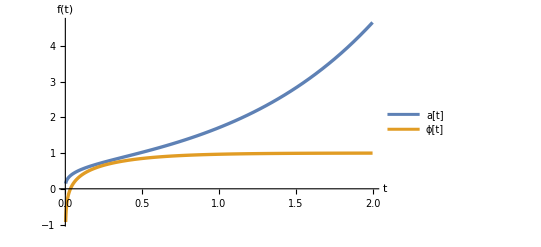

```mathematica
Plot[Evaluate[{a[t],ϕ[t]+1}/.sode1],{t,0.002,2},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotStyle->{Thickness[0.006]},PlotLegends->{"a[t]","ϕ[t]"}]
```

#### 2. Scalar Potential with non-constant V: Part 1

#### First I’ll simplify eqn (1) using the new parameters, → V[ϕ] = m^2 ϕ[t]^2 where m = 1, N = 1, and k = 0 for flat space,

1/𝒩 d/dt((ϕ̇)/𝒩 )+3(ȧ)/(a(𝒩)^2)ϕ̇+1/2(dV/dϕ)=0

d/dt(ϕ̇ )+3(ȧ)/a ϕ̇+1/2 d/dϕ(ϕ^2)=0
ϕ^(..) +3(ȧ)/a ϕ̇+ϕ=0

```mathematica
(* And simplifying eqn (3) with the same paramters *)
```

H=1/2(-OverDot[aa]^2/𝒩^2+(a^3(ϕ̇)^2)/𝒩^2-ka+a^3 V)=0
(-(ȧ)^2+a^2(ϕ̇)^2+a^2 ϕ^2)=0

```mathematica
(* Now we plot them with Dr. McGuigan's initial values and get a similar plot to his *)
sode2=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-1,ϕ'[0.001]==100},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00433326, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

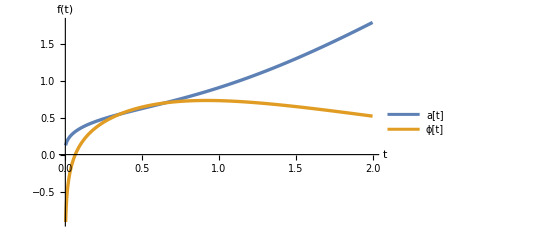

```mathematica
Plot[Evaluate[{a[t],ϕ[t]}/.sode2],{t,0.002,2},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotStyle->{Thickness[0.006]},PlotLegends->{"a[t]","ϕ[t]"}]
```

```mathematica
(* I wanted to include the same plot but using my initial values as well just for comparison *)
sode3=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199999, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

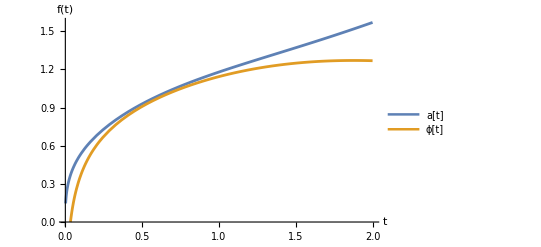

```mathematica
Plot[Evaluate[{a[t],ϕ[t]+1}/.sode3],{t,0.002,2},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotStyle->{Thickness[0.005]},PlotLegends->{"a[t]","ϕ[t]"}]
```

```mathematica
(* It looks almost the same at the very beginning but the overall shapes for both are a bit wonky and ϕ[t] never crosses over a[t] like it does in the previous plot *)
```

#### 3. Scalar Potential with non-constant V: Part 2, Varying small m^2

#### Next, we're going to use eqns 3.56 (1) and 3.54 (3) again but with a different value for V, given by Dr. McGuigan, → V = 1 + 0.1 ϕ^2 (m^2 = 0.1) k = 0 N = 1,

d/dt(ϕ̇ )+3(ȧ)/a ϕ̇+1/2 d/dϕ(1+0.1 ϕ^2)=0
ϕ^(..) +3(ȧ)/a ϕ̇+0.1ϕ=0

#### Then for 3.54 (3),

H=1/2(-OverDot[aa]^2/𝒩^2+(a^3(ϕ̇)^2)/𝒩^2-ka+a^3 V)=0
-(ȧ)^2+a^2(ϕ̇)^2+a^2(1+0.1 ϕ^2)=0
-(ȧ)^2+a^2(ϕ̇)^2+a^2+0.1 a^2 ϕ^2=0
-(ȧ)^2+a^2((ϕ̇)^2+1+0.1 ϕ^2)=0

#### Now we can use NDSolve and plot the two functions again (using my initial conditions),

```mathematica
sode4=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+0.1ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+0.1(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.002, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

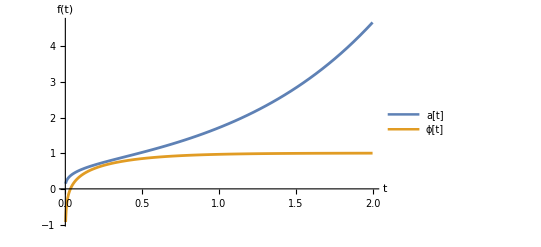

```mathematica
Plot[Evaluate[{a[t],ϕ[t]+1}/.sode4],{t,0.002,2},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotStyle->{Thickness[0.005]},PlotLegends->{"a[t]","ϕ[t]"}]
```

#### → V = 1 + 0.2 ϕ^2 (m^2 = 0.2)

```mathematica
(* I wanted to try to use Manipulate[Plot] so that I could have the little slidey tool that varies m^2 but it didn't work so I'm just going to solve each one and try to plot them all on one graph *)
```

```mathematica
sode5=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+0.2ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+0.2(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.002, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### → V = 1 + 0.3 ϕ^2 (m^2 = 0.3)

```mathematica
sode6=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+0.3ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+0.3(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.002, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### → V = 1 + 0.4 ϕ^2 (m^2 = 0.4)

```mathematica
sode7=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+0.4ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+0.4(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.002, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### → V = 1 + 0.5 ϕ^2 (m^2 = 0.5)

```mathematica
sode8=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+0.5*ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+0.5*(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.002, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### Below is a plot of a[t] and ϕ[t], where m^2 = 0.1, 0.2, 0.3, 0.4, 0.5 just so I could test how to plot all 10 values. I’m not 100% sure that it’s right because they all look exactly the same and overlay on top of each other.

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

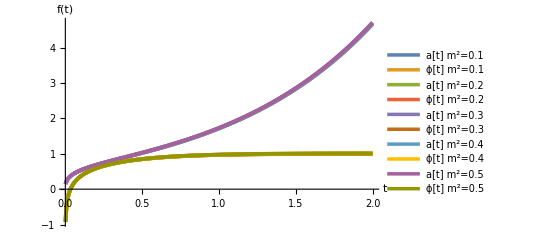

```mathematica
Plot[{Evaluate[{a[t],ϕ[t]+1}/.sode4],Evaluate[{a[t],ϕ[t]+1}/.sode5],Evaluate[{a[t],ϕ[t]+1}/.sode6],Evaluate[{a[t],ϕ[t]+1}/.sode7],Evaluate[{a[t],ϕ[t]+1}/.sode8]},{t,0.002,2},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotStyle->{Thickness[0.007]},PlotLegends->{"a[t] m^2=0.1","ϕ[t] m^2=0.1","a[t] m^2=0.2","ϕ[t] m^2=0.2","a[t] m^2=0.3","ϕ[t] m^2=0.3","a[t] m^2=0.4","ϕ[t] m^2=0.4","a[t] m^2=0.5","ϕ[t] m^2=0.5"}]
```

#### → V = 1 + 0.6 ϕ^2 (m^2 = 0.6)

```mathematica
sode9=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+0.6*ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+0.6*(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199999, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### → V = 1 + 0.7 ϕ^2 (m^2 = 0.7)

```mathematica
sode10=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+0.7*ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+0.7*(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199999, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### → V = 1 + 0.8 ϕ^2 (m^2 = 0.8)

```mathematica
sode11=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+0.8*ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+0.8*(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199999, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### → V = 1 + 0.9 ϕ^2 (m^2 = 0.9)

```mathematica
sode12=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+0.9*ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+0.9*(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199999, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### → V = 1 + ϕ^2 (m^2 = 1)

```mathematica
sode13=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199999, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### Below is a plot of a[t] and ϕ[t], where m^2 = 0.6, 0.7, 0.8, 0.9, 1 . I’m still not 100% sure that it’s right because they all look exactly the same and overlay on top of each other and they look just like the first 0.1 - 0.5 m squares so I’ll ask Dr. McGuigan.

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

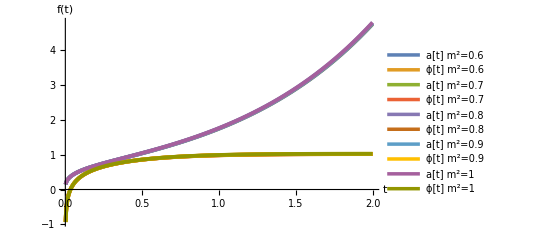

```mathematica
Plot[{Evaluate[{a[t],ϕ[t]+1}/.sode9],Evaluate[{a[t],ϕ[t]+1}/.sode10],Evaluate[{a[t],ϕ[t]+1}/.sode11],Evaluate[{a[t],ϕ[t]+1}/.sode12],Evaluate[{a[t],ϕ[t]+1}/.sode13]},{t,0.002,2},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotStyle->{Thickness[0.007]},PlotLegends->{"a[t] m^2=0.6","ϕ[t] m^2=0.6","a[t] m^2=0.7","ϕ[t] m^2=0.7","a[t] m^2=0.8","ϕ[t] m^2=0.8","a[t] m^2=0.9","ϕ[t] m^2=0.9","a[t] m^2=1","ϕ[t] m^2=1"}]
```

# 4. Scalar Potential with non-constant V: Part 3, Varying larger m^2

#### We’re going to do the same thing as in Section 3: Part 2, but with larger m^2 values, → V = 1 + 2 ϕ^2 (m^2 = 2) k = 0 N = 1,

```mathematica
s1=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+2*ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+2*(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199998, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### → V = 1 + 3 ϕ^2 (m^2 = 3)

```mathematica
s2=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+3*ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+3*(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199997, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### → V = 1 + 4 ϕ^2 (m^2 = 4)

```mathematica
s3=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+4*ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+4*(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199997, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### → V = 1 + 5 ϕ^2 (m^2 = 5)

```mathematica
s4=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+5*ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+5*(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199996, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### → V = 1 + 6 ϕ^2 (m^2 = 6)

```mathematica
s5=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+6*ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+6*(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199995, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### → V = 1 + 7 ϕ^2 (m^2 = 7)

```mathematica
s6=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+7*ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+7*(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199994, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### → V = 1 + 8 ϕ^2 (m^2 = 8)

```mathematica
s7=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+8*ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+8*(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199993, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### → V = 1 + 9 ϕ^2 (m^2 = 9)

```mathematica
s8=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+9*ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+9*(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199992, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### → V = 1 + 10 ϕ^2 (m^2 = 10)

```mathematica
s9=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+10*ϕ[t]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2+10*(a[t])^2(ϕ[t])^2==0,a[0.001]==0.114471,ϕ[0.001]==-2.16743,ϕ'[0.001]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199992, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

#### Now we can plot a[t] and ϕ[t], where m^2 = 1, 2, 3, 4, 5, 6, 7, 8, 9, 10 .

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

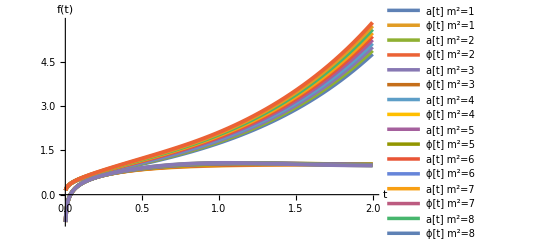

```mathematica
Plot[{Evaluate[{a[t],ϕ[t]+1}/.sode13],Evaluate[{a[t],ϕ[t]+1}/.s1],Evaluate[{a[t],ϕ[t]+1}/.s2],Evaluate[{a[t],ϕ[t]+1}/.s3],Evaluate[{a[t],ϕ[t]+1}/.s4],Evaluate[{a[t],ϕ[t]+1}/.s5],Evaluate[{a[t],ϕ[t]+1}/.s6],Evaluate[{a[t],ϕ[t]+1}/.s7],Evaluate[{a[t],ϕ[t]+1}/.s8],Evaluate[{a[t],ϕ[t]+1}/.s9]},{t,0.002,2},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotStyle->{Thickness[0.007]},PlotLegends->{"a[t] m^2=1","ϕ[t] m^2=1","a[t] m^2=2","ϕ[t] m^2=2","a[t] m^2=3","ϕ[t] m^2=3","a[t] m^2=4","ϕ[t] m^2=4","a[t] m^2=5","ϕ[t] m^2=5","a[t] m^2=6","ϕ[t] m^2=6","a[t] m^2=7","ϕ[t] m^2=7","a[t] m^2=8","ϕ[t] m^2=8","a[t] m^2=9","ϕ[t] m^2=9","a[t] m^2=10","ϕ[t] m^2=10"}]
```

#### So the above graph made me want to plot a[t] and ϕ[t] on separate graphs and also zoom in on the most important parts. Below, I plotted a[t] alone for the different m^2 and then I changed the boundary for t to be 1.2 to 2 so that we could zoom in on the tail section of the graph and closer see the differences between each line.

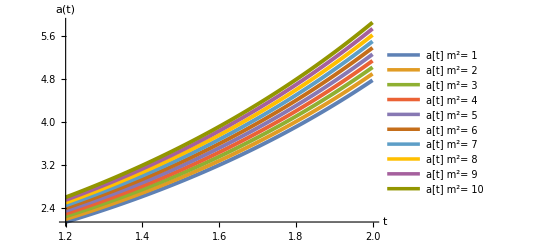

```mathematica
Plot[{Evaluate[{a[t]}/.sode13],Evaluate[{a[t]}/.s1],Evaluate[{a[t]}/.s2],Evaluate[{a[t]}/.s3],Evaluate[{a[t]}/.s4],Evaluate[{a[t]}/.s5],Evaluate[{a[t]}/.s6],Evaluate[{a[t]}/.s7],Evaluate[{a[t]}/.s8],Evaluate[{a[t]}/.s9]},{t,1.2,2},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","a(t)"},PlotStyle->{Thickness[0.007]},PlotLegends->{"a[t]  m^2= 1","a[t]  m^2= 2","a[t]  m^2= 3","a[t]  m^2= 4","a[t]  m^2= 5","a[t]  m^2= 6","a[t] m^2= 7","a[t]  m^2= 8","a[t]  m^2= 9","a[t]  m^2= 10"}]
```

#### Below, I plotted ϕ[t] alone for the different m^2 using a range for t of 0.5 to 2, and I got a cool/weird looking graph that I wasn’t sure matched the original.

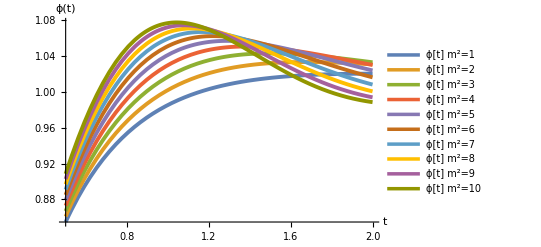

```mathematica
Plot[{Evaluate[{ϕ[t]+1}/.sode13],Evaluate[{ϕ[t]+1}/.s1],Evaluate[{ϕ[t]+1}/.s2],Evaluate[{ϕ[t]+1}/.s3],Evaluate[{ϕ[t]+1}/.s4],Evaluate[{ϕ[t]+1}/.s5],Evaluate[{ϕ[t]+1}/.s6],Evaluate[{ϕ[t]+1}/.s7],Evaluate[{ϕ[t]+1}/.s8],Evaluate[{ϕ[t]+1}/.s9]},{t,0.5,2},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","ϕ(t)"},PlotStyle->{Thickness[0.007]},PlotLegends->{"ϕ[t] m^2=1","ϕ[t] m^2=2","ϕ[t] m^2=3","ϕ[t] m^2=4","ϕ[t] m^2=5","ϕ[t] m^2=6","ϕ[t] m^2=7","ϕ[t] m^2=8","ϕ[t] m^2=9","ϕ[t] m^2=10"}]
```

#### So to check that the above plot was accurate, I plotted the original graph ( both a[t] and ϕ[t] ) and zoomed in on ϕ[t] by changing the range for the y-axis to be 0 to 1.5 . This showed that the above plot for just ϕ[t] alone is correct and also look super cool!!! Like angel hair pasta!

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

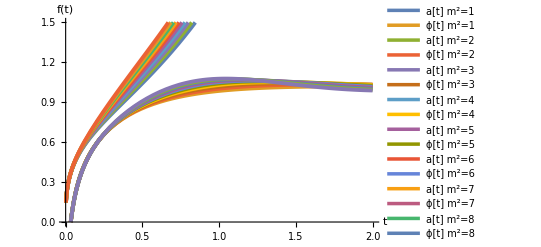

```mathematica
Plot[{Evaluate[{a[t],ϕ[t]+1}/.sode13],Evaluate[{a[t],ϕ[t]+1}/.s1],Evaluate[{a[t],ϕ[t]+1}/.s2],Evaluate[{a[t],ϕ[t]+1}/.s3],Evaluate[{a[t],ϕ[t]+1}/.s4],Evaluate[{a[t],ϕ[t]+1}/.s5],Evaluate[{a[t],ϕ[t]+1}/.s6],Evaluate[{a[t],ϕ[t]+1}/.s7],Evaluate[{a[t],ϕ[t]+1}/.s8],Evaluate[{a[t],ϕ[t]+1}/.s9]},{t,0.002,2},PlotRange->{0,1.5},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotStyle->{Thickness[0.007]},PlotLegends->{"a[t] m^2=1","ϕ[t] m^2=1","a[t] m^2=2","ϕ[t] m^2=2","a[t] m^2=3","ϕ[t] m^2=3","a[t] m^2=4","ϕ[t] m^2=4","a[t] m^2=5","ϕ[t] m^2=5","a[t] m^2=6","ϕ[t] m^2=6","a[t] m^2=7","ϕ[t] m^2=7","a[t] m^2=8","ϕ[t] m^2=8","a[t] m^2=9","ϕ[t] m^2=9","a[t] m^2=10","ϕ[t] m^2=10"}]
```